```mathematica
p1=Flatten[{Table[{x,y},{x,1,3,2},{y,1,7,2}],Table[{x,y},{x,2,4,2},{y,2,8,2}]},2];
p2=Flatten[{Table[{x,y},{x,1,3,2},{y,2,8,2}],Table[{x,y},{x,2,4,2},{y,1,7,2}]},2];
```

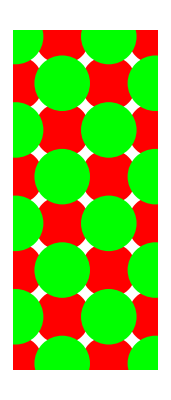

```mathematica
Graphics[{CapForm["Round"],Blue,Thickness[.05],Line[{{1,1},{1,2}}],Line[{{1,3},{1,4}}],Line[{{1,5},{1,6}}],Line[{{1,7},{1,8}}],Line[{{2,2},{2,3}}],Line[{{2,4},{2,5}}],Line[{{2,6},{2,7}}],Line[{{2,8},{3,8}}],Line[{{2,1},{3,1}}],Line[{{3,2},{3,3}}],Line[{{3,4},{3,5}}],Line[{{3,6},{3,7}}],Line[{{4,1},{4,2}}],Line[{{4,3},{4,4}}],Line[{{4,5},{4,6}}],Line[{{4,7},{4,8}}],PointSize[0.1],Red,Point[p1],Green,Point[p2]}]
```

```mathematica
Graphics[{CapForm["Round"],Dashed,Blue,Thickness[.05],Line[{{1,3},{1,2}}],Line[{{1,5},{1,4}}],Line[{{1,7},{1,6}}],Line[{{2,8},{1,8}}],Line[{{2,2},{2,3}}],Line[{{2,4},{2,5}}],Line[{{1,1},{2,1}}],Line[{{3,7},{3,8}}],Line[{{3,2},{3,1}}],Line[{{3,4},{3,3}}],Line[{{3,6},{3,5}}],Line[{{2,6},{2,7}}],Line[{{4,3},{4,2}}],Line[{{4,5},{4,4}}],Line[{{4,7},{4,6}}],Line[{{4,8},{4,8.5}}],Line[{{4,1},{4,0.5}}],PointSize[0.1],Red,Point[p1],Green,Point[p2]}]
```

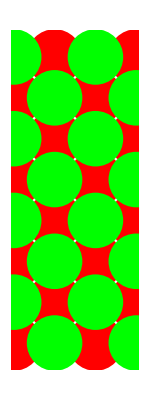

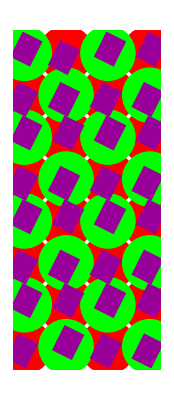

```mathematica
Graphics[{PointSize[0.1],Red,Point[p1],Green,Point[p2],Thickness[0.04],Darker[Magenta,.4],Arrowheads[.15],
Arrow[{{0.9,7.8},{1.2,8.4}}],Arrow[{{2.1,8.2},{1.8,7.6}}],Arrow[{{2.9,7.8},{3.2,8.4}}],Arrow[{{3.9,7.8},{4.2,8.4}}],Arrow[{{1.1,7.2},{0.8,6.6}}],Arrow[{{2.1,7.2},{1.8,6.6}}],Arrow[{{3.1,7.2},{2.8,6.6}}],Arrow[{{4.1,7.2},{3.8,6.6}}],Arrow[{{0.9,5.8},{1.2,6.4}}],Arrow[{{1.9,5.8},{2.2,6.4}}],Arrow[{{2.9,5.8},{3.2,6.4}}],Arrow[{{3.9,5.8},{4.2,6.4}}],Arrow[{{1.1,5.2},{0.8,4.6}}],Arrow[{{2.1,5.2},{1.8,4.6}}],Arrow[{{3.1,5.2},{2.8,4.6}}],Arrow[{{4.1,5.2},{3.8,4.6}}],Arrow[{{0.9,3.8},{1.2,4.4}}],Arrow[{{1.9,3.8},{2.2,4.4}}],Arrow[{{2.9,3.8},{3.2,4.4}}],Arrow[{{3.9,3.8},{4.2,4.4}}],Arrow[{{1.1,3.2},{0.8,2.6}}],Arrow[{{2.1,3.2},{1.8,2.6}}],Arrow[{{3.1,3.2},{2.8,2.6}}],Arrow[{{4.1,3.2},{3.8,2.6}}],Arrow[{{0.9,1.8},{1.2,2.4}}],Arrow[{{1.9,1.8},{2.2,2.4}}],Arrow[{{2.9,1.8},{3.2,2.4}}],Arrow[{{3.9,1.8},{4.2,2.4}}],Arrow[{{1.1,1.2},{0.8,0.6}}],Arrow[{{1.9,0.8},{2.2,1.4}}],Arrow[{{3.1,1.2},{2.8,0.6}}],Arrow[{{4.1,1.2},{3.8,0.6}}]}]
```

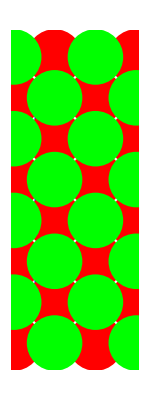

```mathematica
Graphics[{CapForm["Round"],Thickness[.05],Blue,Line[{{1,1},{1,2}}],Line[{{1,3},{1,4}}],Line[{{1,5},{1,6}}],Line[{{1,7},{1,8}}],Line[{{2,8},{3,8}}],Line[{{2,1},{3,1}}],Line[{{3,2},{3,3}}],Line[{{3,4},{3,5}}],Line[{{3,6},{3,7}}],Line[{{4,1},{4,2}}],Line[{{4,3},{4,4}}],Line[{{4,5},{4,6}}],Line[{{4,7},{4,8}}],Circle[{2,2.5},{0.15,0.5},{Pi/2,3Pi/2}],Circle[{2,4.5},{0.15,0.5},{Pi/2,3Pi/2}],Circle[{2,6.5},{0.15,0.5},{Pi/2,3Pi/2}],Dashed,Line[{{1,3},{1,2}}],Line[{{1,5},{1,4}}],Line[{{1,7},{1,6}}],Line[{{2,8},{1,8}}],Line[{{1,1},{2,1}}],Line[{{3,7},{3,8}}],Line[{{3,2},{3,1}}],Line[{{3,4},{3,3}}],Line[{{3,6},{3,5}}],Line[{{4,3},{4,2}}],Line[{{4,5},{4,4}}],Line[{{4,7},{4,6}}],Line[{{4,8},{4,8.5}}],Line[{{4,1},{4,0.5}}],Circle[{2,2.5},{0.15,0.5},{-Pi/2,Pi/2}],Circle[{2,4.5},{0.15,0.5},{-Pi/2,Pi/2}],Circle[{2,6.5},{0.15,0.5},{-Pi/2,Pi/2}],PointSize[0.1],Red,Point[p1],Green,Point[p2]}]
```

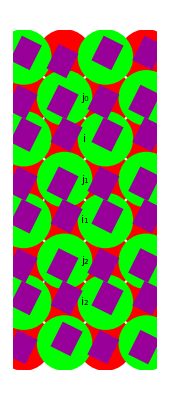

```mathematica
Graphics[{CapForm["Round"],Thickness[.05],Blue,Line[{{1,1},{1,2}}],Line[{{1,3},{1,4}}],Line[{{1,5},{1,6}}],Line[{{1,7},{1,8}}],Line[{{2,8},{3,8}}],Line[{{2,1},{3,1}}],Line[{{3,2},{3,3}}],Line[{{3,4},{3,5}}],Line[{{3,6},{3,7}}],Line[{{4,1},{4,2}}],Line[{{4,3},{4,4}}],Line[{{4,5},{4,6}}],Line[{{4,7},{4,8}}],Circle[{2,2.5},{0.15,0.5},{Pi/2,3Pi/2}],Circle[{2,4.5},{0.15,0.5},{Pi/2,3Pi/2}],Circle[{2,6.5},{0.15,0.5},{Pi/2,3Pi/2}],Dashed,Line[{{1,3},{1,2}}],Line[{{1,5},{1,4}}],Line[{{1,7},{1,6}}],Line[{{2,8},{1,8}}],Line[{{1,1},{2,1}}],Line[{{3,7},{3,8}}],Line[{{3,2},{3,1}}],Line[{{3,4},{3,3}}],Line[{{3,6},{3,5}}],Line[{{4,3},{4,2}}],Line[{{4,5},{4,4}}],Line[{{4,7},{4,6}}],Line[{{4,8},{4,8.5}}],Line[{{4,1},{4,0.5}}],Circle[{2,2.5},{0.15,0.5},{-Pi/2,Pi/2}],Circle[{2,4.5},{0.15,0.5},{-Pi/2,Pi/2}],Circle[{2,6.5},{0.15,0.5},{-Pi/2,Pi/2}],PointSize[.1],Red,Point[p1],Green,Point[p2],Dashing[{}],Thickness[0.04],Darker[Magenta,.4],Arrowheads[.15],
Arrow[{{0.9,7.8},{1.2,8.4}}],Arrow[{{2.1,8.2},{1.8,7.6}}],Arrow[{{2.9,7.8},{3.2,8.4}}],Arrow[{{3.9,7.8},{4.2,8.4}}],Arrow[{{1.1,7.2},{0.8,6.6}}],Arrow[{{2.1,7.2},{1.8,6.6}}],Arrow[{{3.1,7.2},{2.8,6.6}}],Arrow[{{4.1,7.2},{3.8,6.6}}],Arrow[{{0.9,5.8},{1.2,6.4}}],Arrow[{{1.9,5.8},{2.2,6.4}}],Arrow[{{2.9,5.8},{3.2,6.4}}],Arrow[{{3.9,5.8},{4.2,6.4}}],Arrow[{{1.1,5.2},{0.8,4.6}}],Arrow[{{2.1,5.2},{1.8,4.6}}],Arrow[{{3.1,5.2},{2.8,4.6}}],Arrow[{{4.1,5.2},{3.8,4.6}}],Arrow[{{0.9,3.8},{1.2,4.4}}],Arrow[{{1.9,3.8},{2.2,4.4}}],Arrow[{{2.9,3.8},{3.2,4.4}}],Arrow[{{3.9,3.8},{4.2,4.4}}],Arrow[{{1.1,3.2},{0.8,2.6}}],Arrow[{{2.1,3.2},{1.8,2.6}}],Arrow[{{3.1,3.2},{2.8,2.6}}],Arrow[{{4.1,3.2},{3.8,2.6}}],Arrow[{{0.9,1.8},{1.2,2.4}}],Arrow[{{1.9,1.8},{2.2,2.4}}],Arrow[{{2.9,1.8},{3.2,2.4}}],Arrow[{{3.9,1.8},{4.2,2.4}}],Arrow[{{1.1,1.2},{0.8,0.6}}],Arrow[{{1.9,0.8},{2.2,1.4}}],Arrow[{{3.1,1.2},{2.8,0.6}}],Arrow[{{4.1,1.2},{3.8,0.6}}],Black,Text[Style[Subscript[j,0],Large],{2.5,7}],Text[Style[i,Large],{2.5,6}],Text[Style[Subscript[j,1],Large],{2.5,5}],Text[Style[Subscript[i,1],Large],{2.5,4}],Text[Style[Subscript[j,2],Large],{2.5,3}],Text[Style[Subscript[i,2],Large],{2.5,2}]}]
```

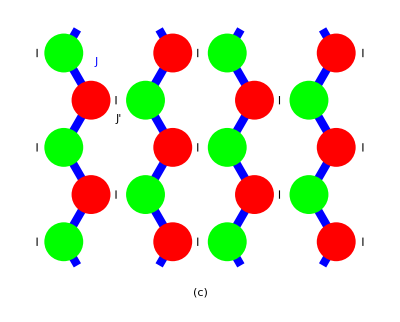

```mathematica
p1=Flatten[{Table[{x,y},{x,0,3,3},{y,0,2Sqrt[3],Sqrt[3]}],Table[{x,y},{x,3/2,9/2,3},{y,Sqrt[3]/2,3Sqrt[3]/2,Sqrt[3]}]},2];
p2=Flatten[{Table[{x,y},{x,1/2,7/2,3},{y,Sqrt[3]/2,3Sqrt[3]/2,Sqrt[3]}],Table[{x,y},{x,2,5,3},{y,0,2Sqrt[3],Sqrt[3]}]},2];
Graphics[{CapForm["Square"],Thickness[.015],Blue,Line[{{1/4,-Sqrt[3]/4},{0,0}}],Line[{{0,0},{1/2,Sqrt[3]/2}}],Line[{{1/2,Sqrt[3]/2},{0,Sqrt[3]}}],Line[{{0,Sqrt[3]},{1/2,3Sqrt[3]/2}}],Line[{{1/2,3Sqrt[3]/2},{0,2Sqrt[3]}}],Line[{{0,2Sqrt[3]},{1/4,9Sqrt[3]/4}}],Line[{{2,0},{3/2,Sqrt[3]/2}}],Line[{{3/2,Sqrt[3]/2},{2,Sqrt[3]}}],Line[{{2,Sqrt[3]},{3/2,3Sqrt[3]/2}}],Line[{{3/2,3Sqrt[3]/2},{2,2Sqrt[3]}}],Line[{{7/4,-Sqrt[3]/4},{2,0}}],Line[{{2,2Sqrt[3]},{7/4,9Sqrt[3]/4}}],Line[{{3,0},{7/2,Sqrt[3]/2}}],Line[{{7/2,Sqrt[3]/2},{3,Sqrt[3]}}],Line[{{3,Sqrt[3]},{7/2,3Sqrt[3]/2}}],Line[{{7/2,3Sqrt[3]/2},{3,2Sqrt[3]}}],Line[{{13/4,-Sqrt[3]/4},{3,0}}],Line[{{3,2Sqrt[3]},{13/4,9Sqrt[3]/4}}],Line[{{5,0},{9/2,Sqrt[3]/2}}],Line[{{9/2,Sqrt[3]/2},{5,Sqrt[3]}}],Line[{{5,Sqrt[3]},{9/2,3Sqrt[3]/2}}],Line[{{9/2,3Sqrt[3]/2},{5,2Sqrt[3]}}],Line[{{19/4,-Sqrt[3]/4},{5,0}}],Line[{{5,2Sqrt[3]},{19/4,9Sqrt[3]/4}}],Dashing[{0.002,0.02}],Black,Line[{{1/2,Sqrt[3]/2},{3/2,Sqrt[3]/2}}],Line[{{1/2,3Sqrt[3]/2},{3/2,3Sqrt[3]/2}}],Line[{{2,0},{3,0}}],Line[{{2,Sqrt[3]},{3,Sqrt[3]}}],Line[{{2,2Sqrt[3]},{3,2Sqrt[3]}}],Line[{{7/2,Sqrt[3]/2},{9/2,Sqrt[3]/2}}],Line[{{7/2,3Sqrt[3]/2},{9/2,3Sqrt[3]/2}}],Line[{{-1/2,0},{0,0}}],Line[{{-1/2,Sqrt[3]},{0,Sqrt[3]}}],Line[{{-1/2,2Sqrt[3]},{0,2Sqrt[3]}}],Line[{{5.5,0},{5,0}}],Line[{{5.5,Sqrt[3]},{5,Sqrt[3]}}],Line[{{5.5,2Sqrt[3]},{5,2Sqrt[3]}}],PointSize[0.07],Green,Point[p1],Red,Point[p2],Blue,Text[Style[J,Large],{0.6,3.3}],Black,Text[Style[J',Large],{1,2.25}],Text[Style["(c)",Large],{2.5,-Sqrt[3]/4-0.5}]}]
```

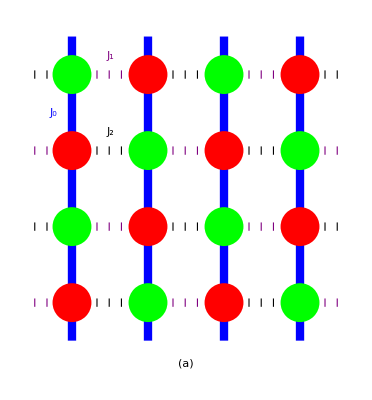

```mathematica
p1=Flatten[{Table[{x,y},{x,1,3,2},{y,1,3,2}],Table[{x,y},{x,2,4,2},{y,2,4,2}]},2];
p2=Flatten[{Table[{x,y},{x,1,3,2},{y,2,4,2}],Table[{x,y},{x,2,4,2},{y,1,3,2}]},2];
Graphics[{CapForm["Square"],Thickness[.015],Blue,Line[{{1,1},{1,2}}],Line[{{1,2},{1,3}}],Line[{{1,3},{1,4}}],Line[{{2,1},{2,2}}],Line[{{2,2},{2,3}}],Line[{{2,3},{2,4}}],Line[{{3,1},{3,2}}],Line[{{3,2},{3,3}}],Line[{{3,3},{3,4}}],Line[{{4,1},{4,2}}],Line[{{4,2},{4,3}}],Line[{{4,3},{4,4}}],Line[{{1,1},{1,1/2}}],Line[{{1,4},{1,9/2}}],Line[{{2,1},{2,1/2}}],Line[{{2,4},{2,9/2}}],Line[{{3,1},{3,1/2}}],Line[{{3,4},{3,9/2}}],Line[{{4,1},{4,1/2}}],Line[{{4,4},{4,9/2}}],Purple,Dashing[{0.002,0.02}],Line[{{2,1},{3,1}}],Line[{{1,2},{2,2}}],Line[{{3,2},{4,2}}],Line[{{2,3},{3,3}}],Line[{{1,4},{2,4}}],Line[{{3,4},{4,4}}],Line[{{1,1},{1/2,1}}],Line[{{1,3},{1/2,3}}],Line[{{4,1},{9/2,1}}],Line[{{4,3},{9/2,3}}],Black,Line[{{1,1},{2,1}}],Line[{{3,1},{4,1}}],Line[{{2,2},{3,2}}],Line[{{1,3},{2,3}}],Line[{{3,3},{4,3}}],Line[{{2,4},{3,4}}],Line[{{1,2},{1/2,2}}],Line[{{1,4},{1/2,4}}],Line[{{4,2},{9/2,2}}],Line[{{4,4},{9/2,4}}],PointSize[0.07],Red,Point[p1],Green,Point[p2],Blue,Text[Style[Subscript[J,0],Large],{0.75,3.5}],Purple,Text[Style[Subscript[J,1],Large],{1.5,4.25}],Black,Text[Style[Subscript[J,2],Large],{1.5,3.25}],Text[Style["(a)",Large],{2.5,0.2}]}]
```